# Sedimentary Clast Shape Parameters Analysis

This notebook is the code Presented in Image Analysis for Quantifying 2D Particle Shape Parameters using Mathematica.
It analyses morphological parameters of objects and presents the data in table and histogram form.

## Set Directory

```mathematica
(*Specify Directory where image files are located *)
SetDirectory["C:\\Users\\Dave\\Documents\\sed parameters"];
```

## Import File

```mathematica
a=image=Import["lst1.bmp"]
(* Check raw image file *)
```

-Graphics-

## Image Preparataion

If the image is not a Grain Boundary Map and is a simple image where grain boundaries can be accurately identified then the following code can be used to create Grain Boundary Maps, otherwise skip this step.

```mathematica
a=image//ColorNegate;
a1=DeleteSmallComponents[a]//ColorNegate;
a2=Dilation[EdgeDetect[a1],-2]//ColorNegate;
a3=SelectComponents[a2,"EnclosingComponentCount",#==0&];
a=Dilation[EdgeDetect[a3],-.5]//ColorNegate
```

-Graphics-

## Grain Detection

Identifies grains and identifies them with labels and best fit circles

```mathematica
grains=SelectComponents[a,"Count",3000<#<100000&]; (*This line sets the size of the objects identified, if unwanted small objects are being identified, increase the 1st value, likewise if oversized objects are being identified lower the 2nd value*)
measures=ComponentMeasurements[grains, {"Centroid", "EquivalentDiskRadius", "Label"}];
"Objects with best fit circles and labels";
Show [a, Graphics[{Blue,Circle @@#&/@ (measures⟦All,2,1;;2⟧),MapThread[Text,{measures⟦All,2,3⟧,measures⟦All,2,1⟧}]}]]
```

-Graphics-

Size Range

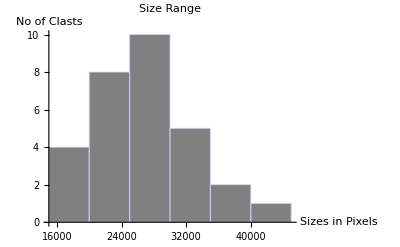

```mathematica
ComponentMeasurements[grains, "Area"];
%/.Rule->List;
sizedata=Last/@% ;
Mean[%];
Histogram[sizedata, AxesLabel->{"Sizes in Pixels","No of Clasts"},PlotLabel->Style["Size Range" ,"Label",16 ,Bold], ChartStyle->{Gray}]
ComponentMeasurements[grains, "LabelCount"];
%/.Rule->List;
Mean[Last/@% ]"Total";
```

Grain Size Distribution

```mathematica
q=Flatten[Quartiles[sizedata]];
q1=Take[q,{1}];
q2=Take[q,{2}];
q3=Take[q,{3}];
mediangrainsize=q2;
sortingcoefficient= √(q3/q1);
skewness=(q1×q3)/q2^2;
Grid[{{Quartiles,Q1,Q2,Q3},{,q1,q2,q3}}, ItemSize->9
,Frame->All]
Grid[{{"Median Grain Size",q2},{"Sorting Coefficient",sortingcoefficient}, {"Skewness",skewness}}, ItemSize->9
,Frame->All]
```

Quartiles | Q1 | Q2 | Q3
 | {23613.3} | {26231.7} | {30257.4}

Median Grain Size | {26231.7}
Sorting Coefficient | {1.13198}
Skewness | {1.03833}

## Shape Parameters

Sphericity/Roundness

Sphericity Calculations (Wadell, 1932)

Mean

0.767219

Min

0.603443

Max

0.859267

All Clasts

0.731332
0.83407
0.719645
0.751822
0.702474
0.843685
0.707559
0.78467
0.754788
0.859267
0.714919
0.819706
0.795143
0.770345
0.837175
0.760823
0.793516
0.603443
0.794017
0.771212
0.824957
0.830639
0.803876
0.822461
0.657151
0.655276
0.786692
0.755036
0.793092
0.718367
0.786618

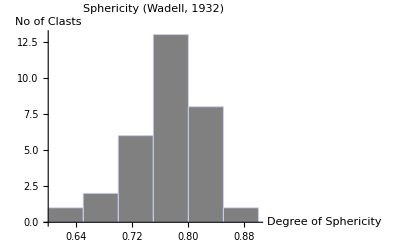

Degree of Circularity Calculations (Wadell, 1932)

Mean

0.477901

Min

0.346979

Max

0.715309

All Clasts

0.538462
0.458999
0.449381
0.412309
0.405423
0.596542
0.346979
0.501099
0.486793
0.415903
0.461613
0.438384
0.715309
0.482088
0.585779
0.494819
0.479057
0.568752
0.456164
0.508305
0.488436
0.395466
0.533531
0.565299
0.379619
0.393566
0.363254
0.433759
0.463092
0.39641
0.60035

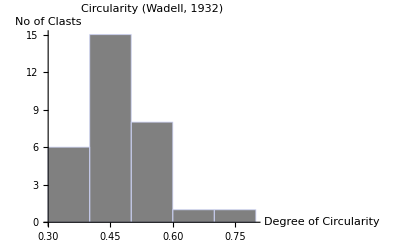

Roundness Calculations (Tickell and Hiatt, 1938)

Mean

0.595371

Min

0.367603

Max

0.743197

All Clasts

0.537517
0.699815
0.520974
0.568413
0.496434
0.715045
0.503839
0.618722
0.57224
0.743197
0.513837
0.675517
0.635653
0.596624
0.703165
0.582889
0.632591
0.367603
0.633745
0.59747
0.683544
0.693366
0.650212
0.679813
0.434657
0.432123
0.621966
0.573492
0.63226
0.518985
0.620791

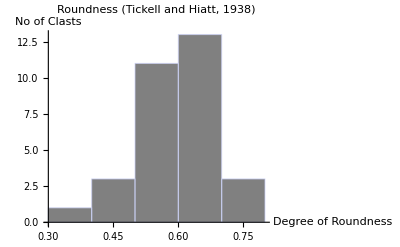

Roundness/Angularity Calculations

Mean

0.67792

Min

0.446504

Max

0.844576

All Clasts

0.5724
0.840464
0.663557
0.673418
0.52047
0.806288
0.490554
0.599341
0.676688
0.813276
0.664722
0.742822
0.757577
0.621129
0.73125
0.764724
0.770911
0.514212
0.667882
0.702046
0.690897
0.732932
0.811583
0.807115
0.446504
0.498909
0.660725
0.647891
0.735815
0.544846
0.844576

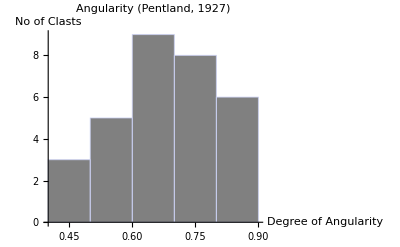

Roundness/Circularity Calculations (Riley, 1941)

Mean

0.23488

Min

0.120394

Max

0.511666

All Clasts

0.289942
0.210681
0.201943
0.169998
0.164368
0.355862
0.120394
0.2511
0.236967
0.172976
0.213087
0.192181
0.511666
0.232409
0.343137
0.244846
0.229496
0.323479
0.208086
0.258374
0.23857
0.156394
0.284656
0.319563
0.14411
0.154894
0.131953
0.188146
0.214454
0.157141
0.36042

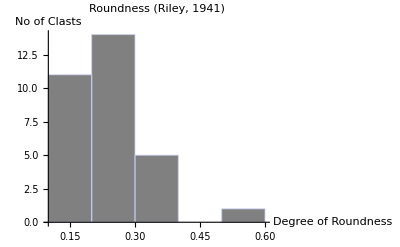

Roughness Calculations

Mean

0.534814

Min

0.400895

Max

0.792227

All Clasts

0.631899
0.493764
0.529016
0.468651
0.471941
0.645989
0.407975
0.547095
0.526839
0.450175
0.518163
0.477357
0.792227
0.541385
0.620004
0.56017
0.533172
0.734888
0.501568
0.560412
0.52067
0.420445
0.589171
0.600944
0.446794
0.461613
0.400895
0.482336
0.511436
0.460867
0.671358

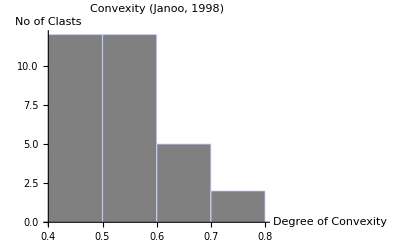

Mean Sphericity | Degree of Circularity | Mean Roundness | Mean Roundness | Mean Roundness | Mean Convexity
0.767219 | 0.477901 | 0.595371 | 0.67792 | 0.23488 | 0.534814

```mathematica
"Sphericity Calculations (Wadell, 1932)"
"Mean"
ComponentMeasurements[grains, "EquivalentDiskRadius"];
%/.Rule->List;
da=(Last/@%)*2  (*Diameter of a circle with the same area as particle*);
ComponentMeasurements[grains, "BoundingDiskRadius"];
%/.Rule->List;
dc=(Last/@%)*2 (*Diameter of the smallest circumscribed circle*);
data =(da/dc);
r2=Mean[%] 
"Min"
Min[data]
"Max"
Max[data]
"All Clasts"
TableForm[data]
l2="Mean Sphericity";
Histogram[data, AxesLabel->{"Degree of Sphericity","No of Clasts"},PlotLabel->Style["Sphericity (Wadell, 1932)" ,"Label",16, Bold], ChartStyle->{Gray}]

"Degree of Circularity Calculations (Wadell, 1932)"
"Mean"
ComponentMeasurements[grains, "Area"];
%/.Rule->List;
pa=(2*(√((Last/@%)/(Pi) )))*(Pi)(*Perimeter of a circle with the same area as particle*);
ComponentMeasurements[grains, "PerimeterLength"];
%/.Rule->List;
pp=Last/@% (*Perimeter of Clast*);
data=pa/pp;
r3=Mean[%] 
"Min"
Min[data]
"Max"
Max[data]
"All Clasts"
TableForm[data]
l3="Degree of Circularity";
Histogram[data, AxesLabel->{"Degree of Circularity","No of Clasts"},PlotLabel->Style["Circularity (Wadell, 1932)" ,"Label",16, Bold], ChartStyle->{Gray}]


"Roundness Calculations (Tickell and Hiatt, 1938)"
"Mean"
ComponentMeasurements[grains, "Area"];
%/.Rule->List;
ap=Last/@%  (*Area of Clast*);
ComponentMeasurements[grains, "BoundingDiskRadius"];
%/.Rule->List;
ac=(Pi)*(Last/@%^2);(*Area of the Smallest Circumscribed Circle*);
data=ap/ac;
r5=Mean[%] 
"Min"
Min[data]
"Max"
Max[data]
"All Clasts"
TableForm[data]
l5="Mean Roundness";
Histogram[data, AxesLabel->{"Degree of Roundness","No of Clasts"},PlotLabel->Style["Roundness (Tickell and Hiatt, 1938)" ,"Label",16, Bold], ChartStyle->{Gray}]



"Roundness/Angularity Calculations" (*a perfect circle should give a value of 1, values trending towards zero refrer to an increase in angularity (Pentland, 1927)*)
"Mean"
ComponentMeasurements[grains, "Area"];
%/.Rule->List;
ap=Last/@%  (*Area of Clast*);
ComponentMeasurements[grains, "Length"];
%/.Rule->List;
ac2=((Last/@%)/(2))^2*(Pi) (*Area of a Circle with a Diameter equal to the longest distance between two points*);
data=ap/ac2;
r6=Mean[%] 
"Min"
Min[data]
"Max"
Max[data]
"All Clasts"
TableForm[data]
l6="Mean Roundness";
Histogram[data, AxesLabel->{"Degree of Angularity","No of Clasts"},
PlotLabel->Style["Angularity (Pentland, 1927)" ,"Label",16, Bold], ChartStyle->{Gray}]

"Roundness/Circularity Calculations (Riley, 1941)"
"Mean"
ComponentMeasurements[grains, "Area"];
%/.Rule->List;
ap=Last/@%  (*Area of Clast*);
ComponentMeasurements[grains, "PerimeterLength"];
%/.Rule->List;
pp=Last/@% (*Perimeter of Clast*);
data=((4*Pi)*(ap))/(pp^2);
r7=Mean[%] 
"Min"
Min[data]
"Max"
Max[data]
"All Clasts"
TableForm[data]
l7="Mean Roundness";
Histogram[data, AxesLabel->{"Degree of Roundness","No of Clasts"},
PlotLabel->Style["Roundness (Riley, 1941)" ,"Label",16, Bold], ChartStyle->{Gray}]



"Roughness Calculations"
"Mean"
(*measure of shape irregularity; tending towards 1 represents a regular shape, while tending towards 0 represents increases in irregularity (Janoo, 1998)*)
ComponentMeasurements[grains, "PerimeterLength"];
%/.Rule->List;
pp=Last/@% (*Perimeter of Clast*);
ComponentMeasurements[grains, "ConvexPerimeterLength"];
%/.Rule->List;
cp=Last/@% (*Convex Perimeter of Clast*);
data=cp/pp;
r8=Mean[%] 
"Min"
Min[data]
"Max"
Max[data]
"All Clasts"
TableForm[data]
l8="Mean Convexity";
Histogram[data, AxesLabel->{"Degree of Convexity","No of Clasts"},PlotLabel->Style["Convexity (Janoo, 1998)" ,"Label",16, Bold], ChartStyle->{Gray}]

Grid[{{l2,l3,l5,l6,l7,l8},{r2,r3,r5,r6,r7,r8}}, ItemSize->7.3
,Frame->All]
```

Elongation, Aspect Ratio and Eccentricity

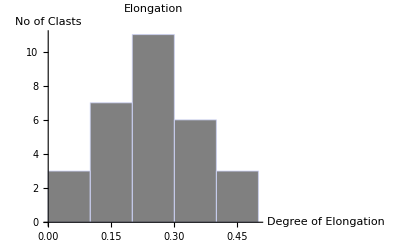

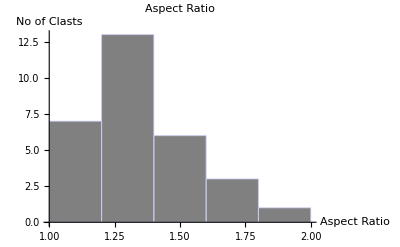

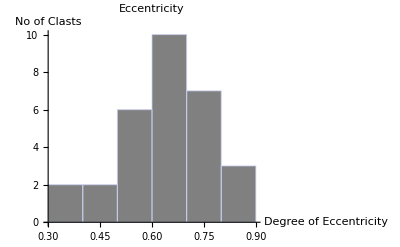

Mean Elongation | Aspect Ratio | Eccentricity
0.25123 | 1.36336 | 0.641686

```mathematica
(*Mean Elongation 1-width/length; closer to 0 perfect sphere, closer to 1 highly elongate*)
ComponentMeasurements[grains, "Elongation"];
%/.Rule->List;
data=Last/@%;
r9=Mean[%];
l9="Mean Elongation";
Histogram[data, AxesLabel->{"Degree of Elongation","No of Clasts"},
PlotLabel->Style["Elongation" ,"Label",16, Bold], ChartStyle->{Gray}]

(*Aspect Ratio*)
ComponentMeasurements[grains, "Length"];
%/.Rule->List;
l=Last/@%;
ComponentMeasurements[grains, "Width"];
%/.Rule->List;
w=Last/@%;
data=l/w;
r10=Mean[%];
l10="Aspect Ratio";
Histogram[data, AxesLabel->{"Aspect Ratio","No of Clasts"},PlotLabel->Style["Aspect Ratio" ,"Label",16, Bold], ChartStyle->{Gray}]

(*Eccentricity => The eccentricity of a circle is zero.The eccentricity of an ellipse which is not a circle is greater than zero but less than 1. The eccentricity of a parabola is 1. The eccentricity of a hyperbola is greater than 1.*)
ComponentMeasurements[grains, "Eccentricity"];
%/.Rule->List;
data=Last/@%;
r11=Mean[%];
l11="Eccentricity";
Histogram[data, AxesLabel->{"Degree of Eccentricity","No of Clasts"},
PlotLabel->Style["Eccentricity" ,"Label",16, Bold], ChartStyle->{Gray}]

Grid[{{l9,l10,l11},{r9,r10,r11}}, ItemSize->7.3
,Frame->All]
```

```mathematica
Grid[{{l2,l3,l5,l6,l7,l8,l9,l10,l11},{r2,r3, r5,r6,r7,r8,r9,r10,r11}}, ItemSize->9
,Frame->All]
```

Mean Sphericity | Degree of Circularity | Mean Roundness | Mean Roundness | Mean Roundness | Mean Convexity | Mean Elongation | Aspect Ratio | Eccentricity
0.767219 | 0.477901 | 0.595371 | 0.67792 | 0.23488 | 0.534814 | 0.25123 | 1.36336 | 0.641686